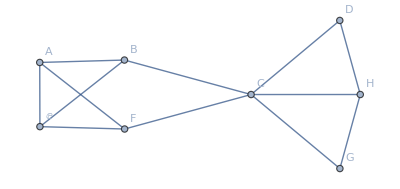

```mathematica
g=Graph[{A<->B,A<->F,A<->E,B<->E,B<->C,C<->F,C<->D,C<->G,C<->H,D<->H,E<->F,H<->G},VertexLabels->"Name"]
```

## Finding Path

```mathematica
FindCycle[g,{5},All]
```

{{F<->C,C<->B,B<->A,A<->ⅇ,ⅇ<->F},{A<->ⅇ,ⅇ<->B,B<->C,C<->F,F<->A}}

```mathematica
FindPath[g,E,B,{3}]
```

{{ⅇ,F,A,B}}

```mathematica
ClearAll[findWalks,findWalksRecur];

(*主函数来查找 walks*)
findWalks[g_,start_,end_,length_]:=Module[{paths},paths=Reap[findWalksRecur[g,start,end,length,{start}]][[2,1]];
Select[paths,Length[#]==length+1&]];

(*辅助递归函数*)
findWalksRecur[g_,start_,end_,0,path_]:=If[start===end,Sow[path],Return[]];

findWalksRecur[g_,start_,end_,length_,path_]:=Module[{neighbors},If[length>0,neighbors=VertexList[NeighborhoodGraph[g,start,{1}]]/. start->Sequence[];
Do[findWalksRecur[g,neighbor,end,length-1,Append[path,neighbor]],{neighbor,neighbors}]]];

(*示例调用*)
findWalks[g,E,B,3]
```

{{ⅇ,B,ⅇ,B},{ⅇ,B,C,B},{ⅇ,B,A,B},{ⅇ,F,ⅇ,B},{ⅇ,F,C,B},{ⅇ,F,A,B},{ⅇ,A,ⅇ,B}}

```mathematica
FindPath[g,G,D,All]
```

{{G,C,D}}

```mathematica
ClearAll[findTrails,findTrailsRecur];

findTrailsRecur[g_,start_,end_,length_,path_,usedEdges_]:=Module[{neighbors},If[length==0,If[start===end,Sow[path]];Return[]];
neighbors=Complement[VertexList[NeighborhoodGraph[g,start,{1}]],{start}];
Do[If[!MemberQ[usedEdges,UndirectedEdge[start,neighbor]]&&!MemberQ[usedEdges,UndirectedEdge[neighbor,start]],findTrailsRecur[g,neighbor,end,length-1,Append[path,neighbor],Append[usedEdges,UndirectedEdge[start,neighbor]]]],{neighbor,neighbors}]];

findTrails[g_,start_,end_,length_]:=Module[{trails},trails=Reap[findTrailsRecur[g,start,end,length,{start},{}]][[2,1]];
trails];
findTrails[g,G,D,8]
ClearAll[findTrails,findTrailsRecur];
```

{{G,C,B,A,ⅇ,F,C,H,D},{G,C,B,ⅇ,A,F,C,H,D},{G,C,F,A,ⅇ,B,C,H,D},{G,C,F,ⅇ,A,B,C,H,D},{G,H,C,B,A,ⅇ,F,C,D},{G,H,C,B,ⅇ,A,F,C,D},{G,H,C,F,A,ⅇ,B,C,D},{G,H,C,F,ⅇ,A,B,C,D}}

To find the ways of forming bipartite graph, we are finding the ways to break all odd-length cycle in the graph. So we Find all cycles.

```mathematica
FindCycle[g,5,All]
```

{{A<->B,B<->ⅇ,ⅇ<->A},{A<->ⅇ,ⅇ<->F,F<->A},{C<->D,D<->H,H<->C},{C<->G,G<->H,H<->C},{F<->C,C<->B,B<->ⅇ,ⅇ<->F},{C<->G,G<->H,H<->D,D<->C},{A<->B,B<->ⅇ,ⅇ<->F,F<->A},{A<->B,B<->C,C<->F,F<->A},{F<->C,C<->B,B<->A,A<->ⅇ,ⅇ<->F},{A<->ⅇ,ⅇ<->B,B<->C,C<->F,F<->A}}

We will break {{A<->B,B<->ⅇ,ⅇ<->A},{A<->ⅇ,ⅇ<->F,F<->A},{C<->D,D<->H,H<->C},{C<->G,G<->H,H<->C}, and {F<->C,C<->B,B<->A,A<->ⅇ,ⅇ<->F},{A<->ⅇ,ⅇ<->B,B<->C,C<->F,F<->A}}.

We find that AE is in all cycles except {C<->D,D<->H,H<->C},{C<->G,G<->H,H<->C}. They both have H<->C, so we can break H<->C to break the rest of odd cycles. Thus we ca make g bipartite by cutting off AE and HC. 
Let’s verify it.

```mathematica
$RecursionLimit = 100000
ClearAll[findTrails,findTrailsRecur];
ClearAll[findTrails,findTrailsRecur];
```

```mathematica
G=Graph[{A<->B,A<->F,B<->E,B<->C,C<->F,C<->D,C<->G,D<->H,E<->F,H<->G},VertexLabels->"Name"]
```

$RecursionLimit::reclim: Recursion depth of 4096 exceeded.

RecursionLimit